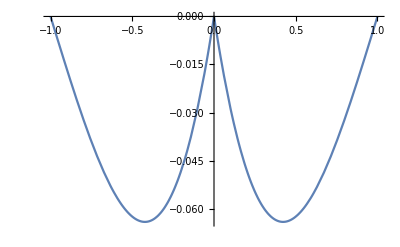

```mathematica
Plot[-1/3 Abs[x]+1/2 Abs[x]^2-1/6 Abs[x]^3,{x,-1,1}]
```

```mathematica
Sum[1/(1+2n)^arst,{n,-∞,∞}]
```

(-4)^-arst (-1+2^arst) ((-2)^arst+2^arst) Zeta[arst]

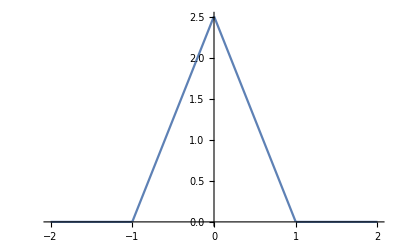

```mathematica
Plot[FourierTransform[Sinc[k/2]^2,k,x],{x,-2,2}]
```

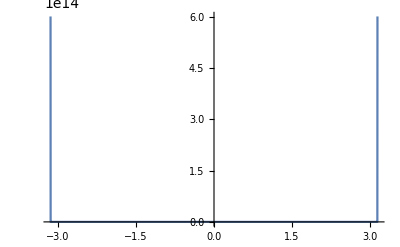

```mathematica
Plot[Sinc[k]^-2,{k,-π,π},PlotRange->Full]
```

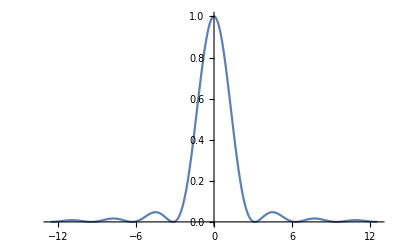

```mathematica
Plot[Sinc[k]^2,{k,-4π,4π},PlotRange->{Full,{0,1}}]
```

```mathematica
Sinc[k]^-2//FunctionExpand
```

```mathematica
FourierTransform[k^2 Csc[k]^2,k,x]
```

ComplexInfinity

```mathematica
FourierTransform[((-1)^n y)/(y-n π),y,x]
```

```mathematica
term[n_,x_]:=(-1)^n (√(2 π) DiracDelta[x]+(ⅈ ⅇ^(ⅈ n π x) n π^(3/2) (Sign[x]-Sign[x] Sign[Abs[Im[n]]]+2 HeavisideTheta[x Sign[Im[n]]] Sign[Im[n]]))/(√2))
```

```mathematica
Sum[term[n,x],{n,-5,5}]//FullSimplify
```

-√(2 π) DiracDelta[x]+√2 π^(3/2) Sign[x] (Sin[π x]-2 Sin[2 π x]+3 Sin[3 π x]-4 Sin[4 π x]+5 Sin[5 π x])

```mathematica
-√(2 π) DiracDelta[x]+
```

```mathematica
FullSimplify[(-1)^n (√(2 π) DiracDelta[x]+(ⅈ ⅇ^(ⅈ n π x) n π^(3/2) (Sign[x]-Sign[x] Sign[Abs[Im[n]]]+2 HeavisideTheta[x Sign[Im[n]]] Sign[Im[n]]))/(√2)),Assumptions->n∈Integers]
```

```mathematica
term2[n_,x_]:=(-1)^n (√(2 π) DiracDelta[x]+(ⅈ ⅇ^(ⅈ n π x) n π^(3/2) Sign[x])/(√2))
```

```mathematica
term2[n,x]+term2[-n,x]//TrigExpand//FullSimplify
```

(-1)^-n √(2 π) DiracDelta[x]+(-1)^n √(2 π) DiracDelta[x]+(ⅈ (-1)^-n ⅇ^(-ⅈ n π x) (-1+ⅇ^(2 ⅈ n π (1+x))) n π^(3/2) Sign[x])/(√2)

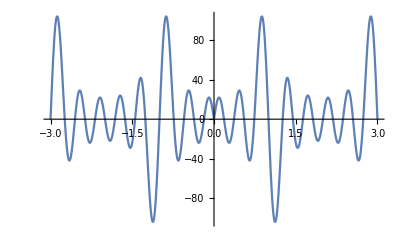

```mathematica
Plot[√2 π^(3/2) Sign[x] (Sin[π x]-2 Sin[2 π x]+3 Sin[3 π x]-4 Sin[4 π x]+5 Sin[5 π x]),{x,-3,3}]
```

```mathematica
Sum[term[n,x],{n,-20,20}]//FullSimplify
```

```mathematica
√(2 π) DiracDelta[x]+Sum[term[n,x],{n,-20,20}]//FullSimplify
```

2 √(2 π) DiracDelta[x]+√2 π^(3/2) Sign[x] (Sin[π x]-2 Sin[2 π x]+3 Sin[3 π x]-4 Sin[4 π x]+5 Sin[5 π x]-6 Sin[6 π x]+7 Sin[7 π x]-8 Sin[8 π x]+9 Sin[9 π x]-10 Sin[10 π x]+11 Sin[11 π x]-12 Sin[12 π x]+13 Sin[13 π x]-14 Sin[14 π x]+15 Sin[15 π x]-16 Sin[16 π x]+17 Sin[17 π x]-18 Sin[18 π x]+19 Sin[19 π x]-20 Sin[20 π x])

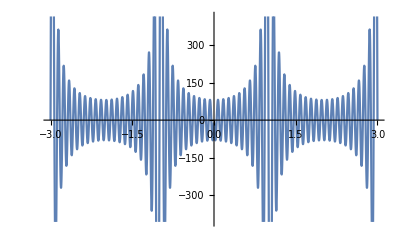

```mathematica
Plot[√2 π^(3/2) Sign[x] (Sin[π x]-2 Sin[2 π x]+3 Sin[3 π x]-4 Sin[4 π x]+5 Sin[5 π x]-6 Sin[6 π x]+7 Sin[7 π x]-8 Sin[8 π x]+9 Sin[9 π x]-10 Sin[10 π x]+11 Sin[11 π x]-12 Sin[12 π x]+13 Sin[13 π x]-14 Sin[14 π x]+15 Sin[15 π x]-16 Sin[16 π x]+17 Sin[17 π x]-18 Sin[18 π x]+19 Sin[19 π x]-20 Sin[20 π x]),{x,-3,3}]
```

```mathematica
sum[x_,nmax_]:=Sign[x]Sum[(-1)^(n+1)n Sin[n π x],{n,1,nmax}]
```

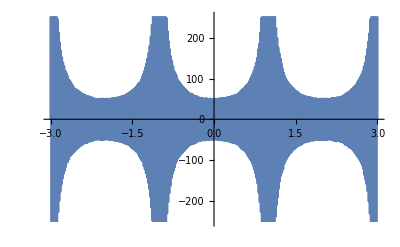

```mathematica
Plot[sum[x,100],{x,-3,3}]
```

```mathematica
(-4)^-arst (-1+2^arst) ((-2)^arst+2^arst)/.arst->2m+2//FullSimplify
```

```mathematica
(-1)^(-2 m) 4^(-1-m) (1+(-1)^(2 m)) (-1+4^(1+m))//Expand
```

1+(-1)^(-2 m)-4^(-1-m)-(-1)^(-2 m) 4^(-1-m)

```mathematica
((-1)^n y)/(y-n π)+((-1)^-n y)/(y+n π)//Expand//Together
```

((-1)^(1-n) y (-n π+(-1)^(2 n) n π+y+(-1)^(2 n) y))/((n π-y) (n π+y))

```mathematica
Series[sum[x,100],{x,0,3}]
```

(-5050 π x+(25499975 π^3 x^3)/3+O[x]^4) Sign[x+O[x]^4]

```mathematica
FourierTransform[Sinc[k]^(1/4),k,x]
```

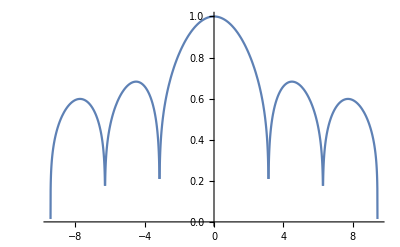

```mathematica
Plot[Abs[Sinc[k]^(1/4)],{k,-3π,3π},PlotRange->{Full,{0,1}}]
```